## Instructions

Evaluating the full Notebook [command A, followed by Shift Enter] produces results based on a pre-loaded sample of parameters. Cells can also be evaluated sequentially. Parts that are not highlighted must be evaluated only once.

Parts in light purple background can be manipulated to change the parameters that are used in the results.

Parts in purple frames are affected by the parameters and should be evaluated [Shift Enter] again after changing the parameters.

Parts in yellow boxes show the output produced

Parts in light grey can be manipulated to observe how changing the parameters affects the output. The parameters used in the results do not change, and no files are generated, but the resulting plots can be saved (Ctrl click on the figure and choose “Save Graphic as...”)

## Initialization

#### These parameters are just an example, and are used to initialize the program

```mathematica
Type={"A","B","C"};
color1=RGBColor[0.1,0.4,0.66];
color2=RGBColor[0.9,0.7,0.2];
color3=RGBColor[0.99,0.2,0.6];
color4=RGBColor[0,0.66,0.56];
colore="CMYKColors";
FitnessColorRescaling=False;
Equilibria=True;
tMAX=200;
c1=0.1;
c2=0.2;
c3=0.3;
nmax=10;
inc={{True,True,True},{True,True,True},{True,True,True}};
bmax={{0,1,1.1},{1,0,0},{1.1,-0.3,0}};
h={{0.3,0.3,0.3},{0.3,0.3,0.3},{0.3,0.3,0.3}};
s={{20,20,20},{20,20,20},{20,20,20}};
```

## Changing the parameters:

#### Type names:

```mathematica
Grid[{{Panel[Style["Enter labels for the three types",Bold,Purple,FontFamily->"Avenir",FontSize->18]]},
{Panel[Style["Type1",FontFamily->"Avenir",FontSize->18]],InputField[Dynamic[Type[[1]]],String],Style[Dynamic[Type[[1]]],Bold,FontFamily->"Avenir",FontSize->18]},{Panel[Style["Type2",FontFamily->"Avenir",FontSize->18]],InputField[Dynamic[Type[[2]]],String],Style[Dynamic[Type[[2]]],Bold,FontFamily->"Avenir",FontSize->18]},{Panel[Style["Type3",FontFamily->"Avenir",FontSize->18]],InputField[Dynamic[Type[[3]]],String],Style[Dynamic[Type[[3]]],Bold,FontFamily->"Avenir",FontSize->18]}},Alignment->Right]
```

Enter labels for the three types |  | 
Type1 |  | 
Type2 |  | 
Type3 |  |

#### Costs:

```mathematica
Grid[{{Panel[Style["Enter costs for the three types",Bold,Purple,FontFamily->"Avenir",FontSize->18]]},{Grid[{{Panel[Style["c_1",FontFamily->"Avenir",FontSize->18]],Slider[Dynamic[c1],{0,1},Appearance->"Labeled"]}}]},{Grid[{{Panel[Style["c_2",FontFamily->"Avenir",FontSize->18]],Slider[Dynamic[c2],{0,1},Appearance->"Labeled"]}}]},
{Grid[{{Panel[Style["c_3",FontFamily->"Avenir",FontSize->18]],Slider[Dynamic[c3],{0,1},Appearance->"Labeled"]}}]}},Alignment->Left]
```

Enter costs for the three types
c_1 |  | 
c_2 |  | 
c_3 |  |

#### Group size:

```mathematica
Grid[{{Panel[Style["Enter group size",Bold,Purple,FontFamily->"Avenir",FontSize->18]],Slider[Dynamic[nmax],{2,100,1},Appearance->"Labeled"]}}]
```

Enter group size |  |

#### Benefit of the effect of X on Y when freq. of X = 1

```mathematica
bx[a_,b_]:=Slider[Dynamic[bmax[[a,b]]],{-10,10},Appearance->"Labeled"]
Grid[{{Panel[Style["Enter b values (the effect of X on Y when the frequency of X is 1)",Bold,Purple,FontFamily->"Avenir",FontSize->18]]},{Table[Grid[{{Panel[Style[Join[ToString[Type[[a]]] " on "<>ToString[Type[[b]]]],FontFamily->"Avenir",FontSize->18]],bx[a,b]}}],{a,1,3},{b,1,3}]//TableForm}},Alignment->Left]
```

Enter b values (the effect of X on Y when the frequency of X is 1)
A  on A |  |  | A  on B |  |  | A  on C |  | 
B  on A |  |  | B  on B |  |  | B  on C |  | 
C  on A |  |  | C  on B |  |  | C  on C |  |

#### h of the effect of X on Y

```mathematica
hx[a_,b_]:=Slider[Dynamic[h[[a,b]]],{0,1},Appearance->"Labeled"]
Grid[{{Panel[Style["Enter h values (the inflection point  for the effect of X on Y)",Bold,Purple,FontFamily->"Avenir",FontSize->18]]},{Table[Grid[{{Panel[Style[Join[ToString[Type[[a]]] " on "<>ToString[Type[[b]]]],FontFamily->"Avenir",FontSize->18]],hx[a,b]}}],{a,1,3},{b,1,3}]//TableForm}},Alignment->Left]
```

Enter h values (the inflection point  for the effect of X on Y)
A  on A |  |  | A  on B |  |  | A  on C |  | 
B  on A |  |  | B  on B |  |  | B  on C |  | 
C  on A |  |  | C  on B |  |  | C  on C |  |

#### s of the effect of X on Y

```mathematica
sx[a_,b_]:=Slider[Dynamic[s[[a,b]]],{0.00001,100},Appearance->"Labeled"]
Grid[{{Panel[Style["Enter s values (the steepness of the effect of X on Y)",Bold,Purple,FontFamily->"Avenir",FontSize->18]]},{Table[Grid[{{Panel[Style[Join[ToString[Type[[a]]] " on "<>ToString[Type[[b]]]],FontFamily->"Avenir",FontSize->18]],sx[a,b]}}],{a,1,3},{b,1,3}]//TableForm}},Alignment->Left]
```

Enter s values (the steepness of the effect of X on Y)
A  on A |  |  | A  on B |  |  | A  on C |  | 
B  on A |  |  | B  on B |  |  | B  on C |  | 
C  on A |  |  | C  on B |  |  | C  on C |  |

#### Whether the effect of X on Y is increasing

```mathematica
inc=Array[True&,{3,3}];
increasingx[a_,b_]:=PopupMenu[Dynamic[inc[[a,b]]],{True,False}]
Grid[{{Panel[Style["Choose whether the benefit functions are increasing",Bold,Purple,FontFamily->"Avenir",FontSize->18]]},{Table[Grid[{{Panel[Style[Join[ToString[Type[[a]]] " on "<>ToString[Type[[b]]]],FontFamily->"Avenir",FontSize->18]],increasingx[a,b]}}],{a,1,3},{b,1,3}]//TableForm}},Alignment->Left]
```

Choose whether the benefit functions are increasing
A  on A |  | A  on B |  | A  on C | 
B  on A |  | B  on B |  | B  on C | 
C  on A |  | C  on B |  | C  on C |

### Writing the parameters on output file

```mathematica
Parameters={
"Types="<>ToString[Table[ToString[Type[[i]]],{i,1,3}]],
"n="<>ToString[nmax],
"c="<>ToString[{c1,c2,c3}],
"b="<>ToString[bmax],
"h="<>ToString[h],
"s="<>ToString[s],
"inc="<>ToString[inc]}//TableForm;
Filename=ToString[Block[{$DateStringFormat={"Year","_","Month","_","Day","_[","Hour","_","Minute","_","Second","]"}},DateString[]]];
Writtenon=Export[NotebookDirectory[]<>ToString[Filename]<>".txt",Parameters,"Table"];
```

```mathematica
Print[Panel[Style["Parameters were written on file: "<>ToString[Writtenon],FontFamily->"Avenir",FontSize->18],Background->LightYellow]]
```

Parameters were written on file: /Users/marcoarchetti/MARCO/PAPERS/GAMES/DeFinetti/2018_10_24_[19_01_51].txt

## Benefit functions

### Plotting the benefit functions

```mathematica
Logistic[from_,to_,n_]:=(1/(1+ⅇ^(s[[from,to]]*(h[[from,to]]-n/nmax)))-1/(1+ⅇ^(s[[from,to]]*(h[[from,to]]-0))))/(1/(1+ⅇ^(s[[from,to]]*(h[[from,to]]-1)))-1/(1+ⅇ^(s[[from,to]]*(h[[from,to]]-0))))
```

```mathematica
V[from_,to_,n_]:=bmax[[from,to]]*If[inc[[from,to]]==True,Logistic[from,to,n],1-Logistic[from,to,n]];
```

```mathematica
Plo[from_,to_]:=Plot[V[from,to,n],{n,0,nmax},
PlotRange->All,
AxesOrigin->{0,0},
PlotLabel->Style[Type[[from]]<>" on "<>Type[[to]],FontFamily->"Avenir",16],
Frame->True,
GridLines->{None,None},
GridLinesStyle->None,
PlotStyle->{Black,Thick},
ImageSize->200,
AspectRatio->1,
FrameLabel->{"n. of "<>Type[[from]]<>" individuals","benefit for "<>Type[[to]]},
FrameStyle->Directive[FontFamily->"Avenir",16],
FrameTicksStyle->Directive[FontFamily->"Avenir",16]]
```

### Benefit functions

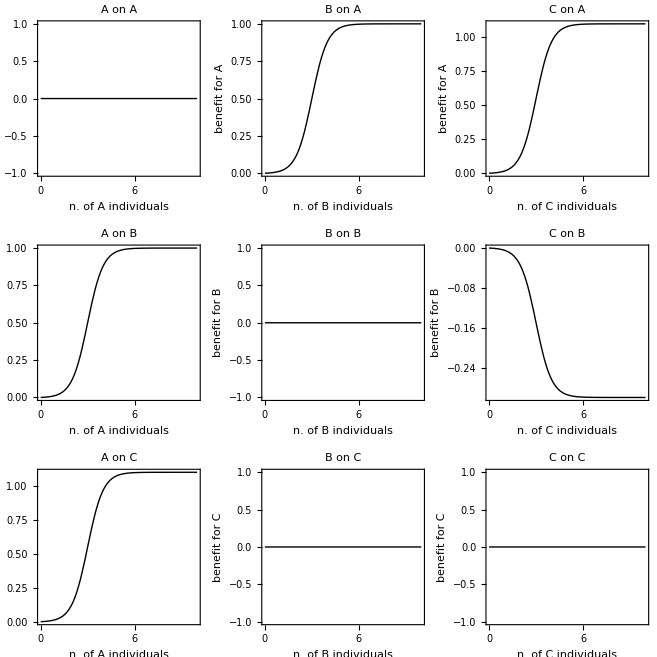

```mathematica
BenefitPlots=GraphicsGrid[Transpose[Table[Plo[from,to],{from,1,3},{to,1,3}]]]
```

```mathematica
Plotsfile=Export[NotebookDirectory[]<>ToString[Filename]<>"_Benefits.pdf",BenefitPlots];
Print[Panel[Style["Plots were saved on file: "<>ToString[Plotsfile],FontFamily->"Avenir",FontSize->18],Background->LightYellow]]
```

Plots were saved on file: /Users/marcoarchetti/MARCO/PAPERS/GAMES/DeFinetti/2018_10_24_[19_01_51]_Benefits.pdf

```mathematica
Export[NotebookDirectory[]<>"Benefits.jpg",BenefitPlots]
```

/Users/marcoarchetti/MARCO/PAPERS/GAMES/DeFinetti/Benefits.jpg

## Dynamics

#### Fitness:

```mathematica
W1[x_,y_,t_]:=∑_(i=0)^(nmax-1) ∑_(j=0)^(nmax-1-i) Multinomial[i,j,nmax-1-i-j](x[t])^i(y[t])^j(1-x[t]-y[t])^(nmax-1-j-i)*(V[1,1,i+1]+V[2,1,j]+V[3,1,nmax-1-i-j]-c1);
W2[x_,y_,t_]:=∑_(i=0)^(nmax-1) ∑_(j=0)^(nmax-1-i) Multinomial[i,j,nmax-1-i-j](x[t])^i(y[t])^j(1-x[t]-y[t])^(nmax-1-j-i)*(V[1,2,i]+V[2,2,j+1]+V[3,2,nmax-1-i-j]-c2);
W3[x_,y_,t_]:=∑_(i=0)^(nmax-1) ∑_(j=0)^(nmax-1-i) Multinomial[i,j,nmax-1-i-j](x[t])^i(y[t])^j(1-x[t]-y[t])^(nmax-1-j-i)*(V[1,3,i]+V[2,3,j]+V[3,3,nmax-i-j]-c3);
```

```mathematica
Wav[x_,y_,t_]:=x[t]*W1[x,y,t]+y[t]*W2[x,y,t]+(1-x[t]-y[t])*W3[x,y,t];
```

#### Generations:

```mathematica
Grid[{{Panel[Style["Choose the number of generations ",Bold,Purple,FontFamily->"Avenir",FontSize->18]],Slider[Dynamic[tMAX],{10,500,1},Appearance->"Labeled"]}}]
```

Choose the number of generations  |  |

#### Recursions:

```mathematica
so[x0_,y0_]:=NDSolve[{
x'[t]==(W1[x,y,t]-Wav[x,y,t])*x[t],
y'[t]==(W2[x,y,t]-Wav[x,y,t])*y[t],
x[0]==x0,
y[0]==y0},
{x,y},{t,0,tMAX}
];
```

```mathematica
Maxo[x0_,y0_]:=Max[Table[Evaluate[Wav[x,y,t]/.so[x0,y0] ],{t,0,tMAX}]]
Mino[x0_,y0_]:=Min[Table[Evaluate[Wav[x,y,t]/.so[x0,y0] ],{t,0,tMAX}]]
```

## Plotting the dynamics over time

#### Colors

```mathematica
Grid[{{Panel[Style["Pick colors for types and fitness",Bold,Purple,FontFamily->"Avenir",FontSize->18]]},{Panel[Style[Type[[1]],FontFamily->"Avenir",FontSize->18]],ColorSlider[Dynamic[color1]]},{Panel[Style[Type[[2]],FontFamily->"Avenir",FontSize->18]],ColorSlider[Dynamic[color2]]},{Panel[Style[Type[[3]],FontFamily->"Avenir",FontSize->18]],ColorSlider[Dynamic[color3]]},{Panel[Style["Fitness",FontFamily->"Avenir",FontSize->18]],ColorSlider[Dynamic[color4]]}},Alignment->Right]
```

Pick colors for types and fitness | 
A | $CellContext`color1
B | $CellContext`color2
C | $CellContext`color3
Fitness | $CellContext`color4

#### Plot

```mathematica
MyLogPlot=Manipulate[LogLinearPlot[Evaluate[{x[t],y[t],1-y[t]-x[t],Rescale[Wav[x,y,t],{Mino[x0,y0],Maxo[x0,y0]}]}/.so[x0,y0] ],{t,0,tMAX},
 PlotStyle->{
Directive[Thick,color1],
Directive[Thick,color2],
Directive[Thick,color3],
Directive[Thick,Dotted,color4]
},
Frame->True,
FrameStyle->Black,
PlotRange->{-0.1,1.1},
FrameLabel->{"generations","frequencies and fitness"},
LabelStyle->Directive[FontFamily->"Avenir",18],
FrameTicks->{{{0,1/4,1/2,3/4,1},None},{Automatic,None}},
GridLines->{Automatic,{0,1/4,1/2,3/4,1}},
GridLinesStyle->Directive[Gray,Opacity[0.5]],
ImageSize->700 ,PlotLabels->{
Style[Type[[1]],FontFamily->"Avenir",18,color1],Style[Type[[2]],FontFamily->"Avenir",18,color2],Style[Type[[3]],FontFamily->"Avenir",18,color3],Style["Fitness",FontFamily->"Avenir",18,color4]}],{{x0,0.33,Style["initial freq. of "<>Type[[1]],FontFamily->"Avenir",18]},0,1},{{y0,0.33,Style["initial freq. of "<>Type[[2]],FontFamily->"Avenir",18]},0,1}]
```

## DeFinetti diagrams

### Data

```mathematica
data[{x0_,y0_}]:=Partition[Flatten[Table[Evaluate[{x[t],y[t],(1-x[t]-y[t])}/.so[x0,y0] ],{t,0,tMAX}]],3];
```

### Coordinate transformation

```mathematica
ternaryToCartesian={1/2 (2 #2+#3)/(#1+#2+#3),Sqrt[3]/2 #3/(#1+#2+#3)}&;
```

### Triangle

```mathematica
background=Graphics[{FaceForm[None],EdgeForm[Gray],Polygon[{{0,0},{1,0},{1/2,Sqrt[3]/2}}],
Inset[Style[Type[[1]],FontFamily->"Avenir",18],{-0.03,-0.03},BaseStyle->Directive[Medium,Bold,Black,FontFamily->"Avenir",14]],
Inset[Style[Type[[2]],FontFamily->"Avenir",18],{1.03,-0.03},BaseStyle->Directive[Medium,Bold,Black,FontFamily->"Avenir",14]],
Inset[Style[Type[[3]],FontFamily->"Avenir",18],{1/2,Sqrt[3]/2+0.03},BaseStyle->Directive[Medium,Bold,Black,FontFamily->"Avenir",14]]}];
```

### Starting points and number of arrows

```mathematica
values={{0.9,0.8,1/3,0.2,0.1},{0.99,0.85,0.66,0.33,0.15,0.01},{0.99,0.83,0.66,0.49,0.33,0.17,0.01}};
```

```mathematica
AllP[spn_]:=Tuples[values[[spn]],{3}]
```

```mathematica
StartingPoints[spn_]:=DeleteCases[Table[Delete[If[0.97<Total[AllP[spn][[i]]]<1.03,AllP[spn][[i]],{0,0,0}],-1],{i,Length[AllP[spn]]}],{0,0}]-0.005;
```

```mathematica
Manipulate[Show[
Table[Graphics[{Gray,JoinForm["Round"],Arrowheads[Table[0.04,{i,1,nx}]],Arrow[ternaryToCartesian@@@data[xx]]}],{xx,StartingPoints[spn]}],
background,AspectRatio->Automatic],{{nx,4,Style["number of arrows",Bold,FontFamily->"Avenir",18]},Range[10]},{{spn,1,Style["amount of starting points",Bold,FontFamily->"Avenir",18]},{1->" Few ",2->" More ",3->" Many "}}]
```

```mathematica
nx=4;Grid[{{Panel[Style["Choose the number of arrows",Bold,Purple,FontFamily->"Avenir",FontSize->18]],Slider[Dynamic[nx],{1,10,1},Appearance->"Labeled"]}}]
```

Choose the number of arrows |  |

```mathematica
spn=2;Grid[{{Panel[Style["Choose the amount of starting points",Bold,Purple,FontFamily->"Avenir",FontSize->18]],SetterBar[Dynamic[spn],{1->" Few ",2->" More ",3->" Many "}]}}]
```

Choose the amount of starting points |  |  |

### Colors for fitness

```mathematica
Grid[{{Panel[Style["Choose color gradient for fitness",Bold,Purple,FontFamily->"Avenir",FontSize->18]],PopupMenu[Dynamic[colore],ColorData["Gradients"],FieldSize->{Automatic,1.6}]},{Framed[Graphics[Raster[{Range[100]/100},ColorFunction->Dynamic[colore]],AspectRatio->.15,ImageSize->290],Background->White,FrameStyle->LightGray,FrameMargins->2,RoundingRadius->5,BaselinePosition->Center]}},Alignment->Left]
```

Choose color gradient for fitness | 
-Graphics- |

```mathematica
Grid[{{Panel[Style["Scaled between fitness minimum and maximum",Bold,Purple,FontFamily->"Avenir",FontSize->18]],PopupMenu[Dynamic[FitnessColorRescaling],{True,False},FieldSize->{Automatic,1.6}]}}]
```

Scaled between fitness minimum and maximum |

```mathematica
AllFitness:=Flatten[Table[Table[Evaluate[Wav[x,y,t]/.so[Extract[xx,1],Extract[xx,2]] ],{t,0,tMAX}],{xx,StartingPoints[spn]}]]
```

```mathematica
If[FitnessColorRescaling==True,Fitnesses=DeleteCases[Flatten[Table[If[x0+y0≤1,Evaluate[Wav[x,y,0]/.so[x0,y0] ]],{x0,0,1,0.1},{y0,0,1,0.1}]],Null]];
```

```mathematica
dataFIT[x0_,y0_]:=Partition[Flatten[Table[Evaluate[{x[t],y[t],(1-x[t]-y[t]),Wav[x,y,t]}/.so[x0,y0] ],{t,0,tMAX}]],4]
```

```mathematica
ColorTable[{x0_,y0_}]:=Table[ColorData[colore][i],{i,If[FitnessColorRescaling==False,dataFIT[x0,y0][[All,4]],Rescale[dataFIT[x0,y0][[All,4]],{Min[Fitnesses],Max[Fitnesses]}]]}]
```

Replace {Min[Fitnesses],Max[Fitnesses]} with {Min[AllFitness],Max[AllFitness]} if you want to rescale based on the maximum and minimum of the trajectories shown, rather than the global minimum and maximum

### Save fitness colors legend on file

```mathematica
FitnessLegend=Grid[{{Null,Style["Fitness",Bold,FontFamily->"Avenir",FontSize->18],Null},{If[FitnessColorRescaling==False,Style[0,FontFamily->"Avenir",FontSize->18],Style[Min[Fitnesses],FontFamily->"Avenir",FontSize->18]],Graphics[Raster[{Range[100]/100},ColorFunction->colore],AspectRatio->.2,ImageSize->200,FrameTicks->All],If[FitnessColorRescaling==False,Style[1,FontFamily->"Avenir",FontSize->18],Style[Max[Fitnesses],FontFamily->"Avenir",FontSize->18]]}}]
```

| Fitness | 
0 | -Graphics- | 1

```mathematica
Legend=Export[NotebookDirectory[]<>ToString[Filename]<>"Legend.pdf",FitnessLegend];
Print[Panel[Style["Legend was saved on file: "<>ToString[Legend],FontFamily->"Avenir",FontSize->18],Background->LightYellow]]
```

Legend was saved on file: /Users/marcoarchetti/MARCO/PAPERS/GAMES/DeFinetti/2018_10_24_[19_01_51]Legend.pdf

```mathematica
Grid[{{Panel[Style["Show the end of the dynamics (possible stable equilibria)",Bold,Purple,FontFamily->"Avenir",FontSize->18]],PopupMenu[Dynamic[Equilibria],{True,False},FieldSize->{Automatic,1.6}]}}]
```

Show the end of the dynamics (possible stable equilibria) |

### Simplex

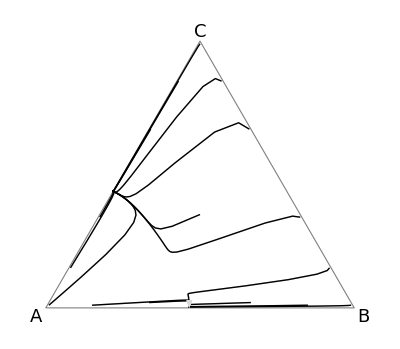

```mathematica
Figure=Show[background,
Table[Graphics[{LightGray,JoinForm["Round"],Arrowheads[Table[0.04,{i,1,nx}]],Arrow[ternaryToCartesian@@@data[xx]]}],{xx,StartingPoints[spn]}],
Table[Graphics[{Thick,JoinForm["Round"],Line[ternaryToCartesian@@@data[xx],VertexColors->ColorTable[xx]]}],{xx,StartingPoints[spn]}],
Table[Graphics[{If[Equilibria==True,Black,Transparent],Disk[Part[ternaryToCartesian@@@data[xx],-1],0.02]}],{xx,StartingPoints[spn]}],
AspectRatio->Automatic]
```

### Save simplex on file

```mathematica
SimplexFig=Export[NotebookDirectory[]<>ToString[Filename]<>"DeFinetti.pdf",Figure];
Print[Panel[Style["Ternary plot was saved on file: "<>ToString[SimplexFig],FontFamily->"Avenir",FontSize->18],Background->LightYellow]]
```

Ternary plot was saved on file: /Users/marcoarchetti/MARCO/PAPERS/GAMES/DeFinetti/2018_10_24_[19_01_51]DeFinetti.pdf

### Additional point

```mathematica
CartesianToTernary={1-#1-#2/(√3),#1-#2/(√3),(2 #2)/(√3)}&;
```

```mathematica
Grid[{{Panel[Style["Click anywhere on the plot to choose an additional starting point",Purple,Bold,FontFamily->"Avenir",FontSize->14]]},{Grid[{{Style["Show previous simplex in the background",Purple,FontFamily->"Avenir",FontSize->14],Checkbox[Dynamic[bkg],{False,True}]}}]},{Manipulate[Show[If[bkg==True,Figure,background],Graphics[{LightGray,JoinForm["Round"],Arrowheads[Table[0.04,{i,1,nx}]],Arrow[ternaryToCartesian@@@data[CartesianToTernary[p[[1]],p[[2]]][[1;;2]]]]}],Graphics[{Thick,JoinForm["Round"],Line[ternaryToCartesian@@@data[CartesianToTernary[p[[1]],p[[2]]][[1;;2]]],VertexColors->ColorTable[CartesianToTernary[p[[1]],p[[2]]][[1;;2]]]]}],Table[Graphics[{If[Equilibria==True,Black,Transparent],Disk[Part[ternaryToCartesian@@@data[CartesianToTernary[p[[1]],p[[2]]][[1;;2]]],-1],0.02]}],{xx,StartingPoints[spn]}],AspectRatio->Automatic],{{p,{1/2,1/(2 √3)}},Locator}]}}]
```

Click anywhere on the plot to choose an additional starting point
Show previous simplex in the background |